# Zero Temperature Physics of the Full Singlet Model

Isaac R. Wang

This code analyze the zero temperature physics of the naturally light singlet scalar model. The interacting potential is chosen to be of the full form. That means the light scalar is regarded as the angular direction of the scalar in the UV theory.

```mathematica
Quit[];
```

```mathematica
$Assumptions={{μH,λ,μS,A,x1,x2,x3,h,v,w,mS,mh,θ,f,f-S,μHsq,μSsq}∈PositiveReals,0<δ<π/2};
MakeBoxes[μSsq,TraditionalForm]:="μ_S^2";
MakeBoxes[μHsq,TraditionalForm]:="μ_H^2";
MakeBoxes[x1,TraditionalForm]:="x_1";
MakeBoxes[x2,TraditionalForm]:="x_2";
MakeBoxes[x3,TraditionalForm]:="x_3";
MakeBoxes[mh,TraditionalForm]:="m_h";
MakeBoxes[mS,TraditionalForm]:="m_S";
```

## Potential

Define the tree-level potential and take the series.

```mathematica
V0=-(μHsq-A f Cos[δ])(H†.H)+λ (H†.H)^2+μSsq f^2(1-Cos[S/f])-A f( (H†.H)-v^2)Cos[S/f-δ];
dof={H->1/(√2){x1+ⅈ x2,h+ⅈ x3}};
truevev={x1->0,x2->0,x3->0};
physical‵vev={h->√2 v,S->0};
Vtree=V0/.dof//Simplify
Vtree‵nogs=Vtree/.truevev//Simplify
```

1/4 (-2 A f cos(S/f-δ) (h^2+x_1^2+x_2^2+x_3^2-2 v^2)-2 (h^2+x_1^2+x_2^2+x_3^2) (μ_H^2-A f cos(δ))-4 f^2 μ_S^2 (cos(S/f)-1)+λ (h^2+x_1^2+x_2^2+x_3^2)^2)

1/4 (-2 A f (h^2-2 v^2) cos(S/f-δ)-2 h^2 (μ_H^2-A f cos(δ))-4 f^2 μ_S^2 (cos(S/f)-1)+h^4 λ)

```mathematica
Vseries=Series[Vtree‵nogs,{S,0,2}]//Normal
```

1/4 S^2 ((A cos(δ) (h^2-2 v^2))/f+2 μ_S^2)+1/4 (4 A f v^2 cos(δ)+h^4 λ-2 h^2 μ_H^2)-1/2 A S sin(δ) (h^2-2 v^2)

```mathematica
Collect[D[Vseries,S],S]
```

1/2 S ((A cos(δ) (h^2-2 v^2))/f+2 μ_S^2)-1/2 A sin(δ) (h^2-2 v^2)

## Tree-level physics

### Mass spectrum

```mathematica
mass‵matrix=D[Vtree,{{x1,x2,x3,h,S},2}]/.truevev//Simplify;
mass‵matrix//MatrixForm
```

(A f cos(δ)-A f cos(S/f-δ)+h^2 λ-μ_H^2 | 0 | 0 | 0 | 0
0 | A f cos(δ)-A f cos(S/f-δ)+h^2 λ-μ_H^2 | 0 | 0 | 0
0 | 0 | A f cos(δ)-A f cos(S/f-δ)+h^2 λ-μ_H^2 | 0 | 0
0 | 0 | 0 | A f cos(δ)-A f cos(S/f-δ)+3 h^2 λ-μ_H^2 | A h sin(S/f-δ)
0 | 0 | 0 | A h sin(S/f-δ) | (A (h^2-2 v^2) cos(S/f-δ))/(2 f)+μ_S^2 cos(S/f))

```mathematica
mStree=Eigenvalues[mass‵matrix[[4;;5,4;;5]]][[1]]//Simplify
mhtree=Eigenvalues[mass‵matrix[[4;;5,4;;5]]][[2]]//Simplify
mgs=mass‵matrix[[1,1]]
```

1/(4 f)(-√((A (2 f^2-h^2+2 v^2) cos(S/f-δ)+2 f (-A f cos(δ)-3 h^2 λ+μ_H^2)-2 f μ_S^2 cos(S/f))^2-4 f (f cos(S/f) (A^2 (h^2-2 v^2)+4 μ_S^2 (3 h^2 λ-μ_H^2))+A (A f (h^2-2 v^2) cos(S/f-2 δ)+A f (h^2+2 v^2) cos((2 S)/f-2 δ)-3 A f h^2+2 A f v^2+2 f^2 μ_S^2 cos(S/f-δ)-2 f^2 μ_S^2 cos((2 S)/f-δ)+2 f^2 μ_S^2 cos(δ+S/f)-2 f^2 μ_S^2 cos(δ)+6 h^4 λ cos(S/f-δ)-2 h^2 μ_H^2 cos(S/f-δ)-12 h^2 λ v^2 cos(S/f-δ)+4 μ_H^2 v^2 cos(S/f-δ))))+2 A f^2 cos(δ)-2 A f^2 cos(S/f-δ)+A h^2 cos(S/f-δ)-2 A v^2 cos(S/f-δ)+6 f h^2 λ+2 f μ_S^2 cos(S/f)-2 f μ_H^2)

1/(4 f)(√((A (2 f^2-h^2+2 v^2) cos(S/f-δ)+2 f (-A f cos(δ)-3 h^2 λ+μ_H^2)-2 f μ_S^2 cos(S/f))^2-4 f (f cos(S/f) (A^2 (h^2-2 v^2)+4 μ_S^2 (3 h^2 λ-μ_H^2))+A (A f (h^2-2 v^2) cos(S/f-2 δ)+A f (h^2+2 v^2) cos((2 S)/f-2 δ)-3 A f h^2+2 A f v^2+2 f^2 μ_S^2 cos(S/f-δ)-2 f^2 μ_S^2 cos((2 S)/f-δ)+2 f^2 μ_S^2 cos(δ+S/f)-2 f^2 μ_S^2 cos(δ)+6 h^4 λ cos(S/f-δ)-2 h^2 μ_H^2 cos(S/f-δ)-12 h^2 λ v^2 cos(S/f-δ)+4 μ_H^2 v^2 cos(S/f-δ))))+2 A f^2 cos(δ)-2 A f^2 cos(S/f-δ)+A h^2 cos(S/f-δ)-2 A v^2 cos(S/f-δ)+6 f h^2 λ+2 f μ_S^2 cos(S/f)-2 f μ_H^2)

A f cos(δ)-A f cos(S/f-δ)+h^2 λ-μ_H^2

```mathematica
physical‵matrix=mass‵matrix[[4;;5,4;;5]]/.physical‵vev//Simplify;
physical‵matrix//MatrixForm
```

(6 λ v^2-μ_H^2 | -√2 A v sin(δ)
-√2 A v sin(δ) | μ_S^2)

The [1,1] and [2,2] term should be positive so that the extremum is minimum, not maximum.

### Vev

We fix the vev of S to be 0. This can be ensured simply by field redefinition.

```mathematica
D[Vtree‵nogs,{{S,h}}]//Simplify
```

{1/2 A (h^2-2 v^2) sin(S/f-δ)+f μ_S^2 sin(S/f),h (A f cos(δ)-A f cos(S/f-δ)+h^2 λ-μ_H^2)}

```mathematica
D[Vtree‵nogs,{{S,h}}]/.{h->√2 v}//Simplify
```

{f μ_S^2 sin(S/f),√2 v (A f cos(δ)-A f cos(S/f-δ)-μ_H^2+2 λ v^2)}

```mathematica
der=D[Vtree‵nogs,{{S,h}}]/.{h->√2 v,S->0}//Simplify
```

{0,√2 v (2 λ v^2-μ_H^2)}

```mathematica
(*cosβ=Cos[β]/.Solve[der[[1]]==0,Cos[β]][[1]]//Normal*)
```

```mathematica
μHsol=Solve[der[[2]]==0,μHsq][[1]]//Normal//Simplify
```

{μ_H^2→2 λ v^2}

For the path of minimizing the S, we have

```mathematica
dVdS=D[Vtree‵nogs,S]//TrigExpand
```

1/2 A h^2 cos(δ) sin(S/f)-1/2 A h^2 sin(δ) cos(S/f)-A v^2 cos(δ) sin(S/f)+A v^2 sin(δ) cos(S/f)+f μ_S^2 sin(S/f)

Make it of the form K sin[S/f+ϕ]. K is positive.

```mathematica
a=Coefficient[dVdS,Sin[S/f]]
b=Coefficient[dVdS,Cos[S/f]]
K=√(a^2+b^2)//Simplify
ϕ=ArcTan[b/a]//Simplify
Spath=-f ϕ
```

1/2 A h^2 cos(δ)-A v^2 cos(δ)+f μ_S^2

A v^2 sin(δ)-1/2 A h^2 sin(δ)

√((1/2 A cos(δ) (h^2-2 v^2)+f μ_S^2)^2+(A v^2 sin(δ)-1/2 A h^2 sin(δ))^2)

-tan^-1((A sin(δ) (h^2-2 v^2))/(A cos(δ) (h^2-2 v^2)+2 f μ_S^2))

f tan^-1((A sin(δ) (h^2-2 v^2))/(A cos(δ) (h^2-2 v^2)+2 f μ_S^2))

#### Potential at vev

```mathematica
Vorigin=Vtree‵nogs/.{S->- f ϕ0,h->0}//TrigExpand
```

-A f v^2 sin(δ) sin(ϕ0)+A f v^2 cos(δ) cos(ϕ0)-f^2 μ_S^2 cos(ϕ0)+f^2 μ_S^2

```mathematica
Vorigin0=Vorigin/.{Sin[ϕ0]->b/K,Cos[ϕ0]->a/K}/.{h->0}//Simplify
```

(f (f μ_S^2 (√(A^2 v^4-2 A f μ_S^2 v^2 cos(δ)+f^2 (μ_S^2)^2)-f μ_S^2)-A^2 v^4+2 A f μ_S^2 v^2 cos(δ)))/(√(A^2 v^4-2 A f μ_S^2 v^2 cos(δ)+f^2 (μ_S^2)^2))

```mathematica
Vorigin0-Vtree‵nogs/.{S->0,h->√2 v}//Simplify
```

(f (f μ_S^2 (√(A^2 v^4-2 A f μ_S^2 v^2 cos(δ)+f^2 (μ_S^2)^2)-f μ_S^2)-A^2 v^4+2 A f μ_S^2 v^2 cos(δ)))/(√(A^2 v^4-2 A f μ_S^2 v^2 cos(δ)+f^2 (μ_S^2)^2))+v^2 (-A f cos(δ)+μ_H^2-λ v^2)

Since we assume that f is very large, we can see cosϕ>0 so that -π/2 < ϕ < π/2.

### Parametrization

Note that this guarantees the [1,1] term of the mass matrix to be 4 λv^2 which is positive-definite.

```mathematica
matrix‵vev=physical‵matrix/.μHsol//Simplify;
matrix‵vev//MatrixForm
```

(4 λ v^2 | -√2 A v sin(δ)
-√2 A v sin(δ) | μ_S^2)

```mathematica
P={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}};
P//MatrixForm
Diag‵mass={{mh^2,0},{0,mS^2}};
Diag‵mass//MatrixForm
rotated=P.Diag‵mass.Inverse[P]//Simplify;
rotated//MatrixForm
```

(cos(θ) | sin(θ)
-sin(θ) | cos(θ))

(m_h^2 | 0
0 | m_S^2)

(1/2 (cos(2 θ) (m_h^2-m_S^2)+m_h^2+m_S^2) | -(sin(θ) cos(θ) (m_h^2-m_S^2))
-(sin(θ) cos(θ) (m_h^2-m_S^2)) | 1/2 (cos(2 θ) (m_S^2-m_h^2)+m_h^2+m_S^2))

```mathematica
sol‵tree=Solve[{rotated[[1,1]]==matrix‵vev[[1,1]],rotated[[1,2]]==matrix‵vev[[1,2]],rotated[[2,2]]==matrix‵vev[[2,2]]},{A,μSsq,λ}][[1]]//Normal//Simplify
```

{A→(csc(δ) sin(θ) cos(θ) (m_h^2-m_S^2))/(√2 v),μ_S^2→1/2 (cos(2 θ) (m_S^2-m_h^2)+m_h^2+m_S^2),λ→(cos(2 θ) (m_h^2-m_S^2)+m_h^2+m_S^2)/(8 v^2)}

```mathematica
μHsol/.sol‵tree
```

{μ_H^2→1/4 (cos(2 θ) (m_h^2-m_S^2)+m_h^2+m_S^2)}

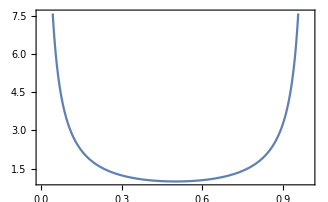

```mathematica
Plot[Csc[δ π],{δ,0,1}]
```

### Benchmark point

```mathematica
num={v->174.,mh->125.13,mS->5,θ->ArcSin[0.08],δ->π/5};
numsol={A,μSsq,λ}/.sol‵tree/.num
```

{8.6187,125.048,0.128464}

```mathematica
μHsq/.μHsol/.sol‵tree/.num
```

7778.73

```mathematica
physical‵matrix‵num=matrix‵vev/.sol‵tree/.num
Eigenvalues[physical‵matrix‵num]^(1/2)
```

(15557.5 | -1246.59
-1246.59 | 125.048)

{125.13,5.}

```mathematica
Vtree‵num=(Vtree‵nogs//TrigExpand)/.μHsol/.sol‵tree/.num/.{f->10000};
```

```mathematica
dVdh=D[Vtree‵num,h]
```

0.128464 h^3-50659.4 h sin(S/10000)-69726.7 h cos(S/10000)+61948. h

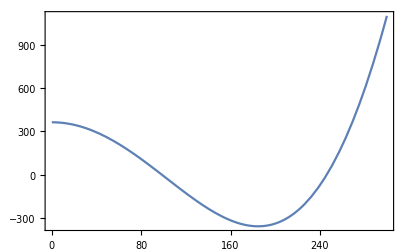

```mathematica
Plot[dVdh/h/.{S->Spath}/.{f->10000,δ->π/5}/.sol‵tree/.num,{h,0,300}]
```

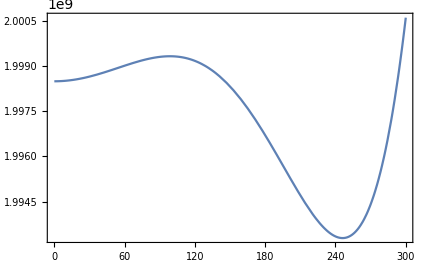

```mathematica
Plot[Vtree‵num/.{S->Spath}/.{f->10000,δ->π/5}/.sol‵tree/.num,{h,0,300}]
```

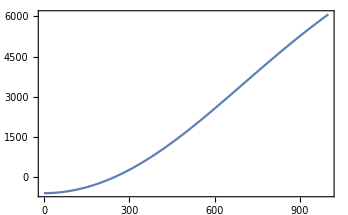

```mathematica
Plot[Spath/.sol‵tree/.num/.{f->10000},{h,0,1000}]
```

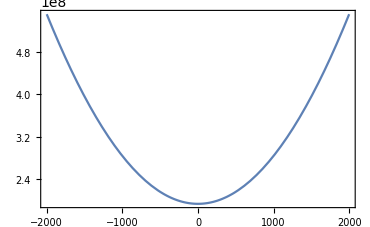

```mathematica
Plot[Vtree‵num/.{h->√2 174.},{S,-2000,2000}]
```

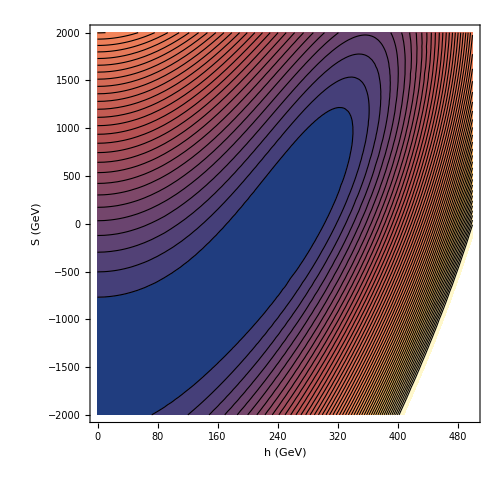

```mathematica
ContourPlot[Vtree‵num,{h,0,500},{S,-2000,2000},Contours->50,BaseStyle->{FontSize->20,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["h (GeV)",FontFamily->"Times",FontSize->20],Style["S (GeV)",FontFamily->"Times",FontSize->20]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->20],ImageSize->500]//CleanRegionPlot
```

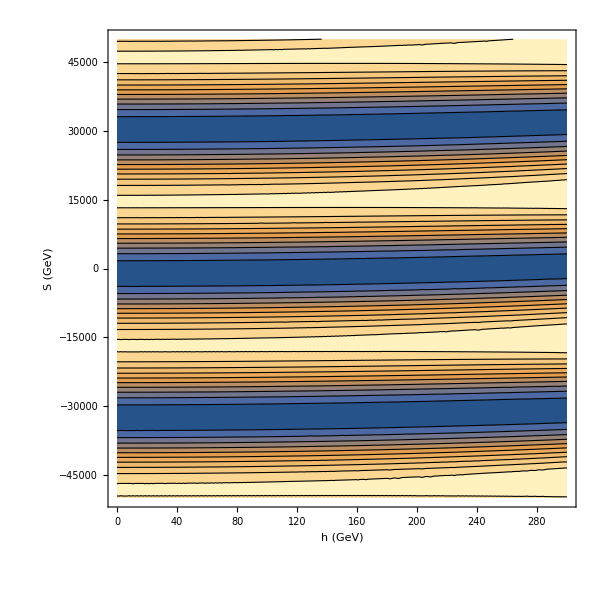

```mathematica
ContourPlot[Vtree‵num,{h,0,300},{S,-5*10^4,5*10^4},Contours->10,BaseStyle->{FontSize->20,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["h (GeV)",FontFamily->"Times",FontSize->20],Style["S (GeV)",FontFamily->"Times",FontSize->20]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->20],ImageSize->600]//CleanRegionPlot
```

Larger S value won’t have new physics information since it’s periodic and equivalent to each other.

### Make sure the local minimum is also global (lower than the origin)

```mathematica
trace=Table[{num={v->174.,mh->125.13,mS->5,θ->ArcSin[0.1],δ->δscan*π,f->4000};
Vtreenum=Vtree‵nogs/.μHsol/.sol‵tree/.num;
Vvev=Vtreenum/.{h->174.*√2,S->0};
Voriginnum=Minimize[Vtreenum/.h->0,S][[1]];
δscan,Voriginnum-Vvev}
,{δscan,1/20,1-1/20,1/20}];
Vdiff[δ_]=Interpolation[trace][δ];
```

```mathematica
FindRoot[Vdiff[δ]==0,{δ,0.3}]
```

{δ→0.326733}

```mathematica
mix‵δ=Table[{trace=Table[{num={v->174.,mh->125.13,mS->5,θ->ArcSin[sinscan],δ->δscan*π};
{Atree,μStree}={A,μSsq}/.sol‵tree/.num;
fc =Atree/μStree(174.)^2 Sin[δscan];
Vtreenum=Vtree‵nogs/.μHsol/.sol‵tree/.num/.{f->3*fc};
Vvev=Vtreenum/.{h->174.*√2,S->0};
Voriginnum=Minimize[Vtreenum/.h->0,S][[1]];
δscan,Voriginnum-Vvev}
,{δscan,1/20,1-1/20,1/20}];
Vdiff[δ_]=Interpolation[trace][δ];
δ0=δ/.FindRoot[Vdiff[δ]==0,{δ,0.3}];
sinscan,δ0}
,{sinscan,0.04,0.2,0.02}];
```

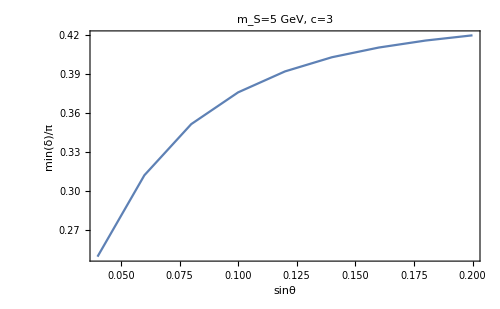

```mathematica
ListLinePlot[mix‵δ,BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,FrameLabel->{Style["sinθ",FontFamily->"Times",FontSize->22],Style["min(δ)/π",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],PlotRangePadding->None,ImageSize->500,PlotLabel->Style["m_S=5 GeV, c=3",FontFamily->"Times",FontSize->26]]
```

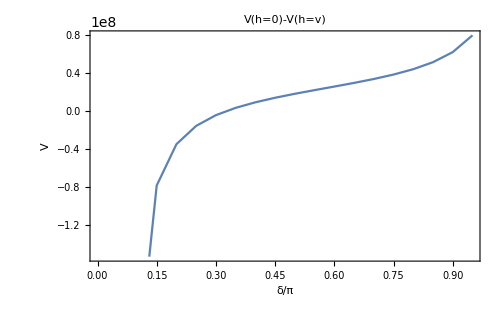

```mathematica
ListLinePlot[trace,BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,FrameLabel->{Style["δ/π",FontFamily->"Times",FontSize->22],Style["V",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],ImageSize->500,PlotLabel->"V(h=0)-V(h=v)"]
```

## 1-loop level physics

### SM MSbar parameters

```mathematica
(*Parameter input and integral definition*)
mW=80.379;
mZ=91.1876;
mt=172.69;
αsmZ=0.1184;
g3mZ=√(4π αsmZ);
GF=1.1663787×10^-5;
vnum=(√2 GF)^(-1/2);
mhpole=125.13;
(*Define integrals. The scale is fixed to be mZ*)
A0[M_]:=M^2(1-Log[M^2/mZ^2]);
B0[p_,M1_,M2_]:=-NIntegrate[Log[(x M1^2+(1-x)M2^2-x(1-x)p^2)/mZ^2],{x,0,1}]
ytmZ=2(GF/(√2)mt^2)^(1/2)+mt/(√2 vnum^3(4π)^2)(-(mhpole^2-4 mt^2)B0[mt,mhpole,mt]+(mt^2(80 mW^2 mZ^2-64 mW^4-7 mZ^4)+40 mW^2 mZ^4-32 mW^4 mZ^2-17 mZ^6)/(9 mt^2 mZ^2)B0[mt,mt,mZ]+(mt^2 mW^2+mt^4-2 mW^4)/mt^2 B0[mt,0,mW]+((3 mhpole^2)/(mhpole^2-mW^2)+2 mW^2/mt^2+3 mW^2/(mW^2-mZ^2)-10)A0[mW]+(3 mW^2/(mW^2-mhpole^2)+1)A0[mhpole]+(36 mt^2 mZ^2-56 mW^2 mZ^2+64 mW^4-17 mZ^4)/(9 mt^2 mZ^2)A0[mt]+((3 mW^2)/(mZ^2-mW^2)+(32 mW^4-40 mW^2 mZ^2+17 mZ^4)/(9 mt^2 mZ^2)-3)A0[mZ]+mhpole^2/2-3 mt^2-9 mW^2+7 mZ^2/18+64 mW^4/(9 mZ^2))+mt/(√2 vnum (4π))αsmZ(-8 A0[mt]/mt^2-8/3)//Re;
g2mZ=2(√2 GF)^(1/2)mW+2 mW/((4π)^2 vnum^3)((mhpole^4/(6 mW^2)-2 mhpole^2/3+2 mW^2)B0[mW,mhpole,mW]+(-mt^4/mW^2-mt^2+2 mW^2)B0[mW,0,mt]+1/6(-48 mW^4/mZ^2+mZ^4/mW^2-68 mW^2+16 mZ^2)B0[mW,mW,mZ]+1/6(mhpole^2(9/(mhpole^2-mW^2)+1/mW^2)+mZ^2/mW^2+mW^2(9/(mW^2-mZ^2)+48/mZ^2)-27)A0[mW]+(2-(mhpole^2(mhpole^2+8 mW^2))/(6 mW^2(mhpole^2-mW^2)))A0[mhpole]+(mt^2/mW^2+1)A0[mt]+1/6(24 mW^2/mZ^2-mZ^2/mW^2+9 mW^2/(mZ^2-mW^2)-17)A0[mW]+1/36(-3 mhpole^2+18 mt^2+288 mW^4/mZ^2-374 mW^2-3 mZ^2))//Re;
g1mZ=2(√2 GF)^(1/2)√(mZ^2-mW^2)+(2 √(mZ^2-mW^2))/((4π)^2 vnum^3)((88/9-(124 mW^2)/(9 mZ^2)+(mhpole^2+34 mW^2)/(6(mZ^2-mW^2)))A0[mZ]+(mhpole^2-4 mW^2)/(2(mhpole^2-mW^2))A0[mhpole]+(-7/9-mt^2/(mZ^2-mW^2)+64 mW^2/(9 mZ^2))A0[mt]+(mhpole^4+2 mW^2(mW^2-15 mZ^2)+3 mhpole^2(2 mW^2+7 mZ^2))/(6(mhpole^2-mW^2)(mW^2-mZ^2))A0[mW]-(mt^4+mW^2 mt^2-2 mW^4)/(mW^2-mZ^2)B0[mW,0,mt]-(mhpole^4-4 mZ^2 mhpole^2+12 mZ^4)/(6(mW^2-mZ^2))B0[mZ,mhpole,mZ]+(mhpole^4-4 mW^2 mhpole^2+12 mW^4)/(6(mW^2-mZ^2))B0[mW,mhpole,mW]+(mZ^6-48 mW^6-68 mZ^2 mW^4+16 mZ^4 mW^2)/(6 mZ^2(mW^2-mZ^2))B0[mW,mW,mZ]+1/9(-23 mW^2+7 mt^2+17 mZ^2-(64 mt^2 mW^2)/mZ^2-(9 mW^2(mt^2-mW^2))/(mZ^2-mW^2))B0[mZ,mt,mt]+(mZ^6-48 mW^6-68 mZ^2 mW^4+16 mZ^4 mW^2)/(6 mZ^2(mZ^2-mW^2))B0[mZ,mW,mW]+1/36(576 mW^4/mZ^2-242 mW^2-3 mhpole^2+257 mZ^2+36 mW^2/(mZ^2-mW^2)+mt^2(82-256 mW^2/mZ^2)))//Re;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.216781}. NIntegrate obtained -1.24537+2.46099 ⅈ and 0.000286423 for the integral and error estimates.

```mathematica
vnum
```

246.22

```mathematica
g1mZ
g2mZ
g3mZ
ytmZ
```

0.357394

0.651016

1.21978

0.977773

### 1-loop potential without scalar contribution

```mathematica
mWsq[h_]:=1/4 g2mZ^2 h^2;
mZsq[h_]:=1/4(g2mZ^2+g1mZ^2)h^2;
mtsq[h_]:=1/2 ytmZ^2 h^2;
VCW[h_]:=1/(64 π^2)(6 mWsq[h]^2(Log[mWsq[h]/mZ^2]-5/6)+3 mZsq[h]^2(Log[mZsq[h]/mZ^2]-5/6)-12 mtsq[h]^2(Log[mtsq[h]/mZ^2]-3/2));
V0Tpre[h_,S_]=(Vtree‵nogs/.{v->v/(√2)}/.{v->vnum})+VCW[h]//Simplify
```

1/4 (A f (121248.-2. h^2) cos(S/f-δ)+2 A f h^2 cos(δ)-4 f^2 μ_S^2 cos(S/f)+4 f^2 μ_S^2+h^4 λ+0.186149 h^4-0.0331527 h^4 log(h)-2 h^2 μ_H^2)

```mathematica
V0Tpre[vnum,S]//Simplify
```

30312.1 A f cos(δ)-f^2 μ_S^2 cos(S/f)+f^2 μ_S^2+9.18821×10^8 λ-30312.1 μ_H^2+3.30987×10^6

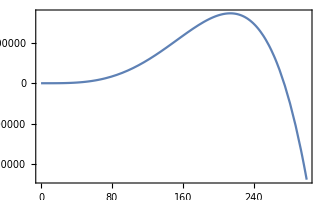

```mathematica
Plot[VCW[h],{h,0,300}]
```

#### 1-loop parametrization

```mathematica
mass‵matrix‵1loop=D[V0Tpre[h,S]//Simplify,{{h,S},2}]/.{h->vnum,S->0};
der‵1loop=D[V0Tpre[h,S],{{h,S}}]/.{h->vnum,S->0}//Simplify;
P={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}};
Diag‵mass={{mhpole^2,0},{0,mS^2}};
rotated=P.Diag‵mass.Inverse[P]//Simplify;
```

```mathematica
mass‵matrix‵1loop
```

(1/4 (727489. λ-4 μ_H^2-11448.4) | -246.22 A sin(δ)
-246.22 A sin(δ) | 1/4 (4 μ_S^2+0.))

```mathematica
der‵1loop
```

{1.49268×10^7 λ-246.22 μ_H^2-69945.5,0.}

#### Benchmark point: mS=5GeV, sinθ=0.1

```mathematica
benchmark={f->5000,θ->ArcSin[0.1],δ->(2π)/5,mS->5.};
mass‵matrix‵1loop‵num=mass‵matrix‵1loop/.benchmark;
rotated‵num=rotated/.benchmark;
der‵1loop‵num=der‵1loop/.benchmark;
```

```mathematica
der‵1loop‵num
```

{1.49268×10^7 λ-246.22 μ_H^2-69945.5,0.}

```mathematica
sol‵1loop=NSolve[{rotated‵num[[1,1]]==mass‵matrix‵1loop‵num[[1,1]],rotated‵num[[1,2]]==mass‵matrix‵1loop‵num[[1,2]],rotated‵num[[2,2]]==mass‵matrix‵1loop‵num[[2,2]],der‵1loop‵num[[1]]==0},{λ,A,μHsq,μSsq}][[1]]
```

{λ→0.149109,A→6.64228,μ_H^2→8755.52,μ_S^2→181.325}

```mathematica
V0T[h_,S_]=V0Tpre[h,S]/.benchmark/.sol‵1loop//Simplify
```

0.0838144 h^4-0.00828818 h^4 log(h)+(1.00671×10^9-16605.7 h^2) sin((S+500 π)/5000)+753.685 h^2-4.53313×10^9 cos(S/5000)+4.53313×10^9

```mathematica
FindRoot[D[V0T[h,S],h]==0&&D[V0T[h,S],S]==0,{h,vnum},{S,0}]
```

{h→246.22,S→0.}

```mathematica
FindMinimum[V0T[h,S],{h,vnum},{S,0}]
```

FindMinimum::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{1.86006×10^8,{h→246.22,S→0.}}

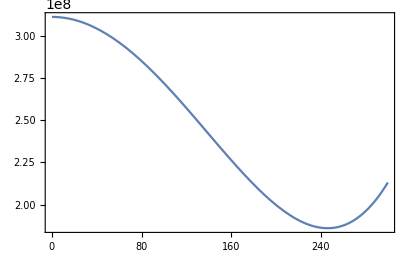

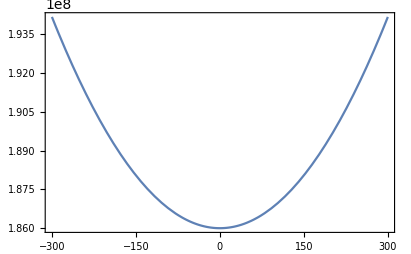

```mathematica
Plot[V0T[h,0],{h,0,300}]
Plot[V0T[vnum,S],{S,-300,300}]
```

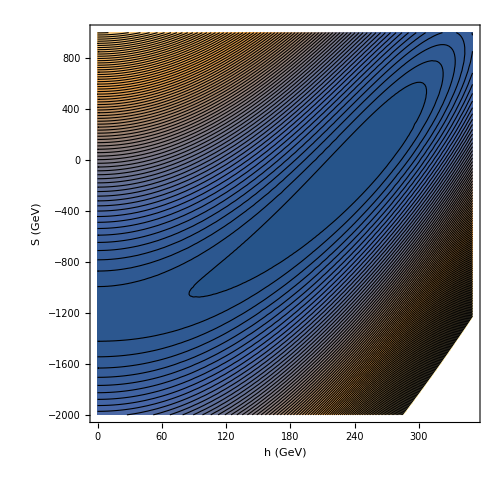

```mathematica
ContourPlot[V0T[h,S],{h,0,350},{S,-2000,1000},Contours->100,BaseStyle->{FontSize->20,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["h (GeV)",FontFamily->"Times",FontSize->20],Style["S (GeV)",FontFamily->"Times",FontSize->20]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->20],ImageSize->500]//CleanRegionPlot
```

```mathematica
mindata=Table[{hscan,Minimize[{V0T[hscan,S],-4000π<S<4000π},S][[1]]},{hscan,10^-5,600,1}];
```

```mathematica
Vloop‵path[h_]=Interpolation[mindata][h];
```

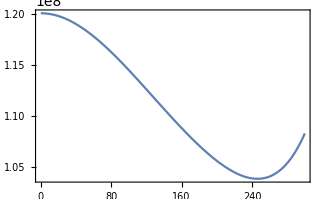

```mathematica
Plot[Vloop‵path[h],{h,10^-5,300}]
```

```mathematica
Minimize[V0T[173000,S],S]
```

{-1.44664×10^19,{S→4624.4}}

2.28888×10^8

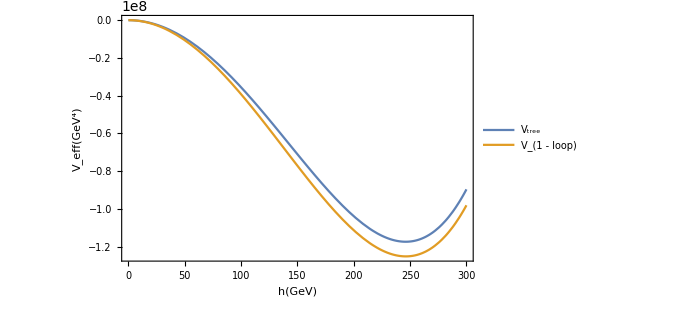

```mathematica
Vtree‵num‵vac=Vtree‵num/.{S->0,h->10^-5}
Plot[{(Vtree‵num/.{S->0})-Vtree‵num‵vac,(V0T[h,0]-V0T[10^-5,0])},{h,0,300},BaseStyle->{FontSize->20,FontFamily->"Times"},Frame->True,FrameLabel->{Style["h(GeV)",FontFamily->"Times",FontSize->20],Style["V_eff(GeV^4)",FontFamily->"Times",FontSize->20]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->20],ImageSize->500,PlotLegends->Placed[{Style["V_tree",FontFamily->"Times",FontSize->22],Style["V_(1 - loop)",FontFamily->"Times",FontSize->22]},Scaled[{0.82,0.75}]]]
```

### 1-loop potential with scalar contribution

#### Potential

```mathematica
mWsq[h_]:=1/4 g2mZ^2 h^2;
mZsq[h_]:=1/4(g2mZ^2+g1mZ^2)h^2;
mtsq[h_]:=1/2 ytmZ^2 h^2;
VCW[h_,S_]:=1/(64 π^2)(6 mWsq[h]^2(Log[mWsq[h]/mZ^2]-5/6)+3 mZsq[h]^2(Log[mZsq[h]/mZ^2]-5/6)-12 mtsq[h]^2(Log[mtsq[h]/mZ^2]-3/2)+3 mgs^2(Log[mgs/mZ^2]-3/2)+mhtree^2(Log[mhtree/mZ^2]-3/2)+mStree^2(Log[mStree/mZ^2]-3/2));
V0Tpre[h_,S_]:=(Vtree‵nogs+VCW[h,S]/.{v->v/(√2)}/.{v->vnum})
```

#### Parametrization

```mathematica
mass‵matrix‵1loop=D[V0Tpre[h,S]//Simplify,{{h,S},2}]/.{h->vnum,S->0};
der‵1loop=D[V0Tpre[h,S],{{h,S}}]/.{h->vnum,S->0};
P={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}};
Diag‵mass={{mhpole^2,0},{0,mS^2}};
rotated=P.Diag‵mass.Inverse[P]//Simplify;
```

#### Benchmark

```mathematica
benchmark={f->5000,θ->ArcSin[0.1],δ->(2π)/5,mS->5};
mass‵matrix‵1loop‵num=mass‵matrix‵1loop/.benchmark//N//Simplify;
rotated‵num=rotated/.benchmark//N//Simplify;
der‵1loop‵num=der‵1loop/.benchmark//N//Simplify;
```

```mathematica
eqns={rotated‵num[[1,1]]==mass‵matrix‵1loop‵num[[1,1]],rotated‵num[[1,2]]==mass‵matrix‵1loop‵num[[1,2]],rotated‵num[[2,2]]==mass‵matrix‵1loop‵num[[2,2]],der‵1loop‵num[[1]]==0};
```

```mathematica
{λ1,A1,μH1,μS1}={λ,A,μHsq,μSsq}/.FindRoot[eqns,{{λ,0.14},{A,11.},{μHsq,8800},{μSsq,200}}]//Re;
sol‵1loop={λ->λ1,A->A1,μHsq->μH1,μSsq->μS1}
```

{λ→0.149505,A→6.69041,μ_H^2→8765.52,μ_S^2→182.513}

```mathematica
V0T[h_,S_]=V0Tpre[h,S]/.benchmark/.sol‵1loop//Re//Simplify;
```

```mathematica
25/μSsq/.sol‵1loop
```

0.136976

Try start with known μS^2.

```mathematica
benchmark={f->5000,μSsq->182.5086696076292,δ->(2π)/5,mS->5};
mass‵matrix‵1loop‵num=mass‵matrix‵1loop/.benchmark//N//Simplify;
rotated‵num=rotated/.benchmark//N//Simplify;
der‵1loop‵num=der‵1loop/.benchmark//N//Simplify;
eqns={rotated‵num[[1,1]]==mass‵matrix‵1loop‵num[[1,1]],rotated‵num[[1,2]]==mass‵matrix‵1loop‵num[[1,2]],rotated‵num[[2,2]]==mass‵matrix‵1loop‵num[[2,2]],der‵1loop‵num[[1]]==0};
```

```mathematica
V0T[h_,S_]=V0Tpre[h,S]/.benchmark/.sol‵1loop//Re//Simplify;
```

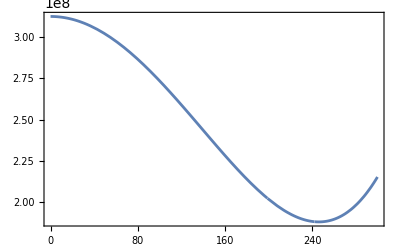

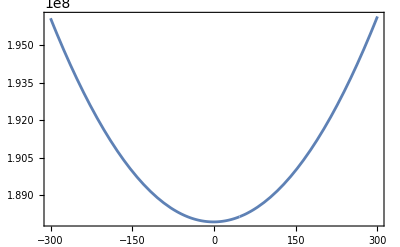

```mathematica
Plot[V0T[h,0],{h,0,300}]
Plot[V0T[vnum,S],{S,-300,300}]
```

```mathematica
FindMinimum[V0T[h,S],{{h,vnum},{S,0}}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{9.88157×10^8,{h→245.999,S→-2.02822}}

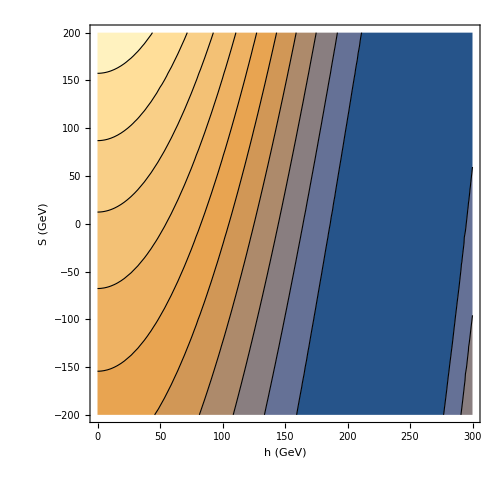

```mathematica
ContourPlot[V0T[h,S],{h,0,300},{S,-200,200},Contours->10,BaseStyle->{FontSize->20,FontFamily->"Times"},Frame->True,BoundaryStyle->None,FrameLabel->{Style["h (GeV)",FontFamily->"Times",FontSize->20],Style["S (GeV)",FontFamily->"Times",FontSize->20]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->20],ImageSize->500]//CleanRegionPlot
```

```mathematica
mindatatree=Table[{hscan,Minimize[{Vtree‵num/.{h->hscan},-10^4<S<10^4},S][[1]]},{hscan,10^-5,300,1}];
mindataloop=Table[{hscan,Minimize[{V0T[hscan,S],-10^4<S<10^4},S][[1]]},{hscan,10^-5,300,1}];
```

```mathematica
Vtree‵path[h_]=Interpolation[mindatatree][h];
Vloop‵path[h_]=Interpolation[mindataloop][h];
```

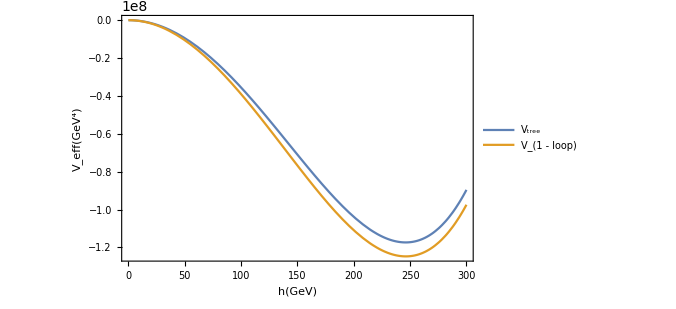

```mathematica
Plot[{(Vtree‵num/.{S->0})-Vtree‵num‵vac,(V0T[h,0]-V0T[10^-5,0])},{h,0,300},BaseStyle->{FontSize->20,FontFamily->"Times"},Frame->True,FrameLabel->{Style["h(GeV)",FontFamily->"Times",FontSize->20],Style["V_eff(GeV^4)",FontFamily->"Times",FontSize->20]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->20],ImageSize->500,PlotLegends->Placed[{Style["V_tree",FontFamily->"Times",FontSize->22],Style["V_(1 - loop)",FontFamily->"Times",FontSize->22]},Scaled[{0.82,0.75}]]]
```

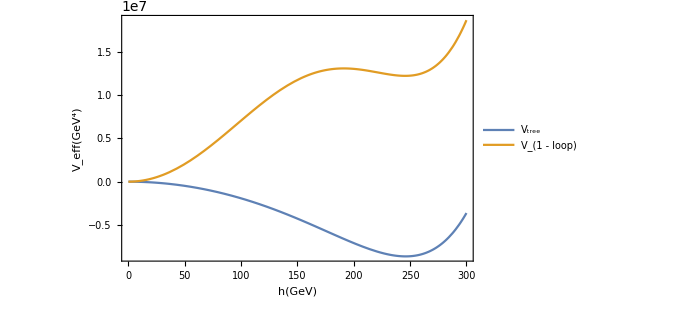

```mathematica
Plot[{(Vtree‵path[h]-Vtree‵path[10^-5]),(Vloop‵path[h]-Vloop‵path[10^-5])},{h,0,300},BaseStyle->{FontSize->20,FontFamily->"Times"},Frame->True,FrameLabel->{Style["h(GeV)",FontFamily->"Times",FontSize->20],Style["V_eff(GeV^4)",FontFamily->"Times",FontSize->20]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->20],ImageSize->500,PlotLegends->Placed[{Style["V_tree",FontFamily->"Times",FontSize->22],Style["V_(1 - loop)",FontFamily->"Times",FontSize->22]},Scaled[{0.82,0.75}]]]
```

#### Local minimum check

Set δ=2π/5 at first

```mathematica
trace=Table[{δinput=(2π)/5;
benchmark={θ->ArcSin[sinscan],δ->δinput,mS->5.0};
{Atree,μStree}={A,μSsq}/.sol‵tree/.benchmark/.{mh->mhpole,v->vnum/(√2)};
fc=Atree/μStree(vnum/(√2))^2;
c=3;
benchmark={θ->ArcSin[sinscan],δ->δinput,mS->5.0,f->c*fc};
mass‵matrix‵1loop‵num=mass‵matrix‵1loop/.benchmark//N//Simplify;
rotated‵num=rotated/.benchmark//N//Simplify;
der‵1loop‵num=der‵1loop/.benchmark//N//Simplify;
eqns={rotated‵num[[1,1]]==mass‵matrix‵1loop‵num[[1,1]],rotated‵num[[1,2]]==mass‵matrix‵1loop‵num[[1,2]],rotated‵num[[2,2]]==mass‵matrix‵1loop‵num[[2,2]],der‵1loop‵num[[1]]==0};
sol‵1loop=FindRoot[eqns,{{λ,0.14},{A,1.2Atree},{μHsq,8800},{μSsq,0.8μStree}}];
V0T[h_,S_]=V0Tpre[h,S]/.sol‵1loop/.benchmark//Re//Simplify;
Vvev=NMinimize[V0T[vnum,S],S][[1]];
Vorigin=NMinimize[V0T[10^-5,S],S][[1]];
sinscan,Vorigin-Vvev
}
,{sinscan,0.2,0.3,0.01}]
```

(0.2 | 2.68479×10^6
0.21 | 2.28744×10^6
0.22 | 1.94851×10^6
0.23 | 1.65891×10^6
0.24 | 1.41131×10^6
0.25 | 1.19972×10^6
0.26 | 1.01922×10^6
0.27 | 865753.
0.28 | 735934.
0.29 | 626928.
0.3 | 536349.)

OK almost fine everywhere.

```mathematica
trace=Table[{δinput=π/5;
mSinput=1;
sinscan=mSinput*ratio;
benchmark={θ->ArcSin[sinscan],δ->δinput,mS->mSinput};
{Atree,μStree}={A,μSsq}/.sol‵tree/.benchmark/.{mh->mhpole,v->vnum/(√2)};
fc=Atree/μStree(vnum/(√2))^2;
c=30;
benchmark={θ->ArcSin[sinscan],δ->δinput,mS->mSinput,f->c*fc};
mass‵matrix‵1loop‵num=mass‵matrix‵1loop/.benchmark//N//Simplify;
rotated‵num=rotated/.benchmark//N//Simplify;
der‵1loop‵num=der‵1loop/.benchmark//N//Simplify;
eqns={rotated‵num[[1,1]]==mass‵matrix‵1loop‵num[[1,1]],rotated‵num[[1,2]]==mass‵matrix‵1loop‵num[[1,2]],rotated‵num[[2,2]]==mass‵matrix‵1loop‵num[[2,2]],der‵1loop‵num[[1]]==0};
sol‵1loop=FindRoot[eqns,{{λ,0.14},{A,1.2Atree},{μHsq,8800},{μSsq,0.8μStree}}];
V0T[h_,S_]=V0Tpre[h,S]/.sol‵1loop/.benchmark//Re//Simplify;
Vvev=NMinimize[V0T[vnum,S],S][[1]];
Vorigin=NMinimize[V0T[10^-5,S],S][[1]];
ratio,Vorigin-Vvev
}
,{ratio,0.06,0.06,0.002}]
```

(0.06 | 5.9387×10^6)

```mathematica
func[rt_]=Interpolation[trace][rt];
FindRoot[func[x]==0,{x,0.01}]
```

{x→0.0153989}

Conclusion: this is similar to SFOPT bound: sin is proportioanl to m_S. For fixed c and δ, every bounds are straight lines with fixed slopes.

#### Scans

Here we do more parameter scans according to what kind of plot do we want.

```mathematica
renormalize[mSinput_,sinθ_,δinput_,finput_]:=Block[{benchmark,mass‵matrix‵1loop‵num,rotated‵num,der‵1loop‵num,Atree,μStree,λtree,μHtree,sol‵1loop,λmsbar,Amsbar,μhsqmsbar,μSsqmsbar},
benchmark={f->finput,θ->ArcSin[sinθ],δ->δinput,mS->mSinput,mh->mhpole,v->vnum/(√2)};
mass‵matrix‵1loop‵num=mass‵matrix‵1loop/.benchmark;
rotated‵num=rotated/.benchmark;
der‵1loop‵num=der‵1loop/.benchmark;
{Atree,μStree,λtree}={A,μSsq,λ}/.sol‵tree/.benchmark;
μHtree=μHsq/.μHsol/.sol‵tree/.benchmark;
sol‵1loop=FindRoot[{rotated‵num[[1,1]]==mass‵matrix‵1loop‵num[[1,1]],rotated‵num[[1,2]]==mass‵matrix‵1loop‵num[[1,2]],rotated‵num[[2,2]]==mass‵matrix‵1loop‵num[[2,2]],der‵1loop‵num[[1]]==0},{{λ,1.4λtree},{A,0.7Atree},{μHsq,8000},{μSsq,μStree}}];
λmsbar=λ/.sol‵1loop//Re;
Amsbar=A/.sol‵1loop//Re;
μhsqmsbar=μHsq/.sol‵1loop//Re;
μSsqmsbar=μSsq/.sol‵1loop//Re;
Return[{λmsbar,Amsbar,μhsqmsbar,μSsqmsbar}]
]
```

```mathematica
AbsoluteTiming[renormalize[5,0.1,π/5,10^4]]
```

{0.02386,{0.149505,10.8252,8765.52,182.523}}

```mathematica
renorm‵μS[mSinput_,μSinput_,δinput_,finput_]:=Block[{benchmark,mass‵matrix‵1loop‵num,rotated‵num,der‵1loop‵num,sol‵1loop,λmsbar,Amsbar,μhsqmsbar,μSsqmsbar,sinθ},
benchmark={f->finput,μSsq->μSinput,δ->δinput,mS->mSinput,mh->mhpole,v->vnum/(√2)};
mass‵matrix‵1loop‵num=mass‵matrix‵1loop/.benchmark;
rotated‵num=rotated/.benchmark;
der‵1loop‵num=der‵1loop/.benchmark;
sol‵1loop=FindRoot[{rotated‵num[[1,1]]==mass‵matrix‵1loop‵num[[1,1]],rotated‵num[[1,2]]==mass‵matrix‵1loop‵num[[1,2]],rotated‵num[[2,2]]==mass‵matrix‵1loop‵num[[2,2]],der‵1loop‵num[[1]]==0},{{λ,0.1},{A,0.2*(1-mSinput^2/μSinput)},{μHsq,8000},{θ,0.1}}];
λmsbar=λ/.sol‵1loop//Re;
Amsbar=A/.sol‵1loop//Re;
μhsqmsbar=μHsq/.sol‵1loop//Re;
sinθ=Sin[θ/.sol‵1loop//Re];
Return[{λmsbar,Amsbar,μhsqmsbar,sinθ}]
]
```

```mathematica
renorm‵μS[5,182.512,2π/5,10^4]
```

{0.149505,6.6905,8765.52,0.100001}

Scan for the PT parameter scanning.

```mathematica
c30‵δ2π5‵GeV=Flatten[Table[{
c=30;
sinθ=sinscan;
δinput=(2π)/5;
num={θ->ArcSin[sinθ],δ->δinput,mS->mSscan,mh->mhpole,v->vnum/(√2)};
{Atree,μStree,λtree}={A,μSsq,λ}/.sol‵tree/.num;
fc =Atree/μStree(vnum/(√2))^2 Sin[δinput];
{λmsbar,Amsbar,μhsqmsbar,μSsqmsbar}=renormalize[mSscan,sinθ,δinput,c*fc];
ye=(√2)/vnum*5.11*10^-4;
eEDM=Amsbar/(c*fc)*ye/((16 π^2)^2)(√2)/vnum 1/(5.06*10^13)Sin[δinput];
nEDM=1/(3 √2)0.938/174(5.11*10^-4)/(c*fc)sinθ 1/mSscan^2;
V0T[h_,S_]=V0Tpre[h,S]/.{λ->λmsbar,A->Amsbar,μHsq->μhsqmsbar,μSsq->μSsqmsbar,f->c*fc,δ->δinput};
Vorigin=Minimize[V0T[10^-5,S]//Re,S][[1]];
Vvev=V0T[vnum,0];
mSscan,sinθ,λmsbar,Amsbar,μhsqmsbar,μSsqmsbar, c*fc,Vorigin-Vvev,eEDM,nEDM},
{mSscan,1,10,0.5},{sinscan,0.02,0.1,0.002}],1];
```

```mathematica
Export[NotebookDirectory[]<>"output/c30_delta_2pi5_GeV_param.csv",c30‵δ2π5‵GeV];
```

```mathematica
c3‵δ2π5‵GeV=Flatten[Table[{
c=3;
sinθ=sinscan;
δinput=(2π)/5;
num={θ->ArcSin[sinθ],δ->δinput,mS->mSscan,mh->mhpole,v->vnum/(√2)};
{Atree,μStree,λtree}={A,μSsq,λ}/.sol‵tree/.num;
fc =Atree/μStree(vnum/(√2))^2 Sin[δinput];
{λmsbar,Amsbar,μhsqmsbar,μSsqmsbar}=renormalize[mSscan,sinθ,δinput,c*fc];
ye=(√2)/vnum*5.11*10^-4;
eEDM=Amsbar/(c*fc)*ye/((16 π^2)^2)(√2)/vnum 1/(5.06*10^13)Sin[δinput];
nEDM=1/(3 √2)0.938/174(5.11*10^-4)/(c*fc)sinθ 1/mSscan^2;
V0T[h_,S_]=V0Tpre[h,S]/.{λ->λmsbar,A->Amsbar,μHsq->μhsqmsbar,μSsq->μSsqmsbar,f->c*fc,δ->δinput};
Vorigin=Minimize[V0T[10^-5,S]//Re,S][[1]];
Vvev=V0T[vnum,0];
mSscan,sinθ,λmsbar,Amsbar,μhsqmsbar,μSsqmsbar, c*fc,Vorigin-Vvev,eEDM,nEDM},
{mSscan,1,10,0.5},{sinscan,0.02,0.1,0.002}],1];
```

```mathematica
Export[NotebookDirectory[]<>"output/c3_delta_2pi5_GeV_param.csv",c3‵δ2π5‵GeV];
```

```mathematica
c30‵δπ5‵GeV=Flatten[Table[{
c=30;
sinθ=sinscan;
δinput=π/5;
num={θ->ArcSin[sinθ],δ->δinput,mS->mSscan,mh->mhpole,v->vnum/(√2)};
{Atree,μStree,λtree}={A,μSsq,λ}/.sol‵tree/.num;
fc =Atree/μStree(vnum/(√2))^2 Sin[δinput];
{λmsbar,Amsbar,μhsqmsbar,μSsqmsbar}=renormalize[mSscan,sinθ,δinput,c*fc];
ye=(√2)/vnum*5.11*10^-4;
eEDM=Amsbar/(c*fc)*ye/((16 π^2)^2)(√2)/vnum 1/(5.06*10^13)Sin[δinput];
nEDM=1/(3 √2)0.938/174(5.11*10^-4)/(c*fc)sinθ 1/mSscan^2;
V0T[h_,S_]=V0Tpre[h,S]/.{λ->λmsbar,A->Amsbar,μHsq->μhsqmsbar,μSsq->μSsqmsbar,f->c*fc,δ->δinput};
Vorigin=Minimize[V0T[10^-5,S]//Re,S][[1]];
Vvev=V0T[vnum,0];
mSscan,sinθ,λmsbar,Amsbar,μhsqmsbar,μSsqmsbar, c*fc,Vorigin-Vvev,eEDM,nEDM},
{mSscan,1,31,2},{sinscan,0.01,0.15,0.002}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Export[NotebookDirectory[]<>"output/c30_delta_pi5_GeV_param.csv",c30‵δπ5‵GeV];
```

```mathematica
c3‵δπ5‵GeV=Flatten[Table[{
c=3;
sinθ=sinscan;
δinput=π/5;
num={θ->ArcSin[sinθ],δ->δinput,mS->mSscan,mh->mhpole,v->vnum/(√2)};
{Atree,μStree,λtree}={A,μSsq,λ}/.sol‵tree/.num;
fc =Atree/μStree(vnum/(√2))^2 Sin[δinput];
{λmsbar,Amsbar,μhsqmsbar,μSsqmsbar}=renormalize[mSscan,sinθ,δinput,c*fc];
ye=(√2)/vnum*5.11*10^-4;
eEDM=Amsbar/(c*fc)*ye/((16 π^2)^2)(√2)/vnum 1/(5.06*10^13)Sin[δinput];
nEDM=1/(3 √2)0.938/174(5.11*10^-4)/(c*fc)sinθ 1/mSscan^2;
V0T[h_,S_]=V0Tpre[h,S]/.{λ->λmsbar,A->Amsbar,μHsq->μhsqmsbar,μSsq->μSsqmsbar,f->c*fc,δ->δinput};
Vorigin=Minimize[V0T[10^-5,S]//Re,S][[1]];
Vvev=V0T[vnum,0];
mSscan,sinθ,λmsbar,Amsbar,μhsqmsbar,μSsqmsbar, c*fc,Vorigin-Vvev,eEDM,nEDM},
{mSscan,1,31,2},{sinscan,0.01,0.15,0.002}],1];
```

```mathematica
Export[NotebookDirectory[]<>"output/c3_delta_pi5_GeV_param.csv",c3‵δπ5‵GeV];
```

```mathematica
c12‵δpi20‵GeV=Flatten[Table[{
sinθ=sinscan;
δinput=π/20;
c=1.2*1/Sin[δinput];
num={θ->ArcSin[sinθ],δ->δinput,mS->mSscan,mh->mhpole,v->vnum/(√2)};
{Atree,μStree,λtree}={A,μSsq,λ}/.sol‵tree/.num;
fc =Atree/μStree(vnum/(√2))^2 Sin[δinput];
{λmsbar,Amsbar,μhsqmsbar,μSsqmsbar}=renormalize[mSscan,sinθ,δinput,c*fc];
ye=(√2)/vnum*5.11*10^-4;
eEDM=Amsbar/(c*fc)*ye/((16 π^2)^2)(√2)/vnum 1/(5.06*10^13)Sin[δinput];
nEDM=1/(3 √2)0.938/174(5.11*10^-4)/(c*fc)sinθ 1/mSscan^2;
V0T[h_,S_]=V0Tpre[h,S]/.{λ->λmsbar,A->Amsbar,μHsq->μhsqmsbar,μSsq->μSsqmsbar,f->c*fc,δ->δinput};
Vorigin=Minimize[V0T[10^-5,S]//Re,S][[1]];
Vvev=V0T[vnum,0];
mSscan,sinθ,λmsbar,Amsbar,μhsqmsbar,μSsqmsbar, c*fc,Vorigin-Vvev,eEDM,nEDM},
{mSscan,1,41,2},{sinscan,0.004,0.15,0.002}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Export[NotebookDirectory[]<>"output/c12_delta_pi20_GeV_param.csv",c12‵δpi20‵GeV];
```

```mathematica
c15‵δpi20‵GeV=Flatten[Table[{
sinθ=sinscan;
δinput=π/20;
c=1.5*1/Sin[δinput];
num={θ->ArcSin[sinθ],δ->δinput,mS->mSscan,mh->mhpole,v->vnum/(√2)};
{Atree,μStree,λtree}={A,μSsq,λ}/.sol‵tree/.num;
fc =Atree/μStree(vnum/(√2))^2 Sin[δinput];
{λmsbar,Amsbar,μhsqmsbar,μSsqmsbar}=renormalize[mSscan,sinθ,δinput,c*fc];
ye=(√2)/vnum*5.11*10^-4;
eEDM=Amsbar/(c*fc)*ye/((16 π^2)^2)(√2)/vnum 1/(5.06*10^13)Sin[δinput];
nEDM=1/(3 √2)0.938/174(5.11*10^-4)/(c*fc)sinθ 1/mSscan^2;
V0T[h_,S_]=V0Tpre[h,S]/.{λ->λmsbar,A->Amsbar,μHsq->μhsqmsbar,μSsq->μSsqmsbar,f->c*fc,δ->δinput};
Vorigin=Minimize[V0T[10^-5,S]//Re,S][[1]];
Vvev=V0T[vnum,0];
mSscan,sinθ,λmsbar,Amsbar,μhsqmsbar,μSsqmsbar, c*fc,Vorigin-Vvev,eEDM,nEDM},
{mSscan,1,41,2},{sinscan,0.004,0.15,0.002}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Export[NotebookDirectory[]<>"output/c15_delta_pi20_GeV_param.csv",c15‵δpi20‵GeV];
```

```mathematica
c30‵δ2π5‵MeV=Flatten[Table[{
c=30;
sinθ=sinscan;
δinput=(2π)/5;
num={θ->ArcSin[sinθ],δ->δinput,mS->mSscan,mh->mhpole,v->vnum/(√2)};
{Atree,μStree,λtree}={A,μSsq,λ}/.sol‵tree/.num;
fc =Atree/μStree(vnum/(√2))^2 Sin[δinput];
{λmsbar,Amsbar,μhsqmsbar,μSsqmsbar}=renormalize[mSscan,sinθ,δinput,c*fc];
ye=(√2)/vnum*5.11*10^-4;
eEDM=Amsbar/(c*fc)*ye/((16 π^2)^2)(√2)/vnum 1/(5.06*10^13)Sin[δinput];
nEDM=1/(3 √2)0.938/174(5.11*10^-4)/(c*fc)sinθ 1/mSscan^2;
V0T[h_,S_]=V0Tpre[h,S]/.{λ->λmsbar,A->Amsbar,μHsq->μhsqmsbar,μSsq->μSsqmsbar,f->c*fc,δ->δinput};
Vorigin=Minimize[V0T[10^-5,S]//Re,S][[1]];
Vvev=V0T[vnum,0];
mSscan,sinθ,λmsbar,Amsbar,μhsqmsbar,μSsqmsbar, c*fc,Vorigin-Vvev,eEDM,nEDM},
{mSscan,2*10^-3,18.0*10^-3,1*10^-3},{sinscan,0.01*10^-3,0.3*10^-3,0.005*10^-3}],1];
```

```mathematica
Export[NotebookDirectory[]<>"output/c30_delta_2pi5_MeV_param.csv",c30‵δ2π5‵MeV];
```

```mathematica
c3‵δ2π5‵MeV=Flatten[Table[{
c=3;
sinθ=sinscan;
δinput=(2π)/5;
num={θ->ArcSin[sinθ],δ->δinput,mS->mSscan,mh->mhpole,v->vnum/(√2)};
{Atree,μStree,λtree}={A,μSsq,λ}/.sol‵tree/.num;
fc =Atree/μStree(vnum/(√2))^2 Sin[δinput];
{λmsbar,Amsbar,μhsqmsbar,μSsqmsbar}=renormalize[mSscan,sinθ,δinput,c*fc];
ye=(√2)/vnum*5.11*10^-4;
eEDM=Amsbar/(c*fc)*ye/((16 π^2)^2)(√2)/vnum 1/(5.06*10^13)Sin[δinput];
nEDM=1/(3 √2)0.938/174(5.11*10^-4)/(c*fc)sinθ 1/mSscan^2;
V0T[h_,S_]=V0Tpre[h,S]/.{λ->λmsbar,A->Amsbar,μHsq->μhsqmsbar,μSsq->μSsqmsbar,f->c*fc,δ->δinput};
Vorigin=Minimize[V0T[10^-5,S]//Re,S][[1]];
Vvev=V0T[vnum,0];
mSscan,sinθ,λmsbar,Amsbar,μhsqmsbar,μSsqmsbar, c*fc,Vorigin-Vvev,eEDM,nEDM},
{mSscan,2*10^-3,18*10^-3,1*10^-3},{sinscan,0.01*10^-3,0.3*10^-3,0.005*10^-3}],1];
```

```mathematica
Export[NotebookDirectory[]<>"output/c3_delta_2pi5_MeV_param.csv",c3‵δ2π5‵MeV];
```

```mathematica
c30‵δπ5‵MeV=Flatten[Table[{
c=30;
sinθ=sinscan;
δinput=π/5;
num={θ->ArcSin[sinθ],δ->δinput,mS->mSscan,mh->mhpole,v->vnum/(√2)};
{Atree,μStree,λtree}={A,μSsq,λ}/.sol‵tree/.num;
fc =Atree/μStree(vnum/(√2))^2 Sin[δinput];
{λmsbar,Amsbar,μhsqmsbar,μSsqmsbar}=renormalize[mSscan,sinθ,δinput,c*fc];
ye=(√2)/vnum*5.11*10^-4;
eEDM=Amsbar/(c*fc)*ye/((16 π^2)^2)(√2)/vnum 1/(5.06*10^13)Sin[δinput];
nEDM=1/(3 √2)0.938/174(5.11*10^-4)/(c*fc)sinθ 1/mSscan^2;
V0T[h_,S_]=V0Tpre[h,S]/.{λ->λmsbar,A->Amsbar,μHsq->μhsqmsbar,μSsq->μSsqmsbar,f->c*fc,δ->δinput};
Vorigin=Minimize[V0T[10^-5,S]//Re,S][[1]];
Vvev=V0T[vnum,0];
mSscan,sinθ,λmsbar,Amsbar,μhsqmsbar,μSsqmsbar, c*fc,Vorigin-Vvev,eEDM,nEDM},
{mSscan,2*10^-3,40*10^-3,2*10^-3},{sinscan,0.02*10^-3,0.2*10^-3,0.002*10^-3}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Export[NotebookDirectory[]<>"output/c30_delta_pi5_MeV_param.csv",c30‵δπ5‵MeV];
```

```mathematica
c3‵δπ5‵MeV=Flatten[Table[{
c=3;
sinθ=sinscan;
δinput=π/5;
num={θ->ArcSin[sinθ],δ->δinput,mS->mSscan,mh->mhpole,v->vnum/(√2)};
{Atree,μStree,λtree}={A,μSsq,λ}/.sol‵tree/.num;
fc =Atree/μStree(vnum/(√2))^2 Sin[δinput];
{λmsbar,Amsbar,μhsqmsbar,μSsqmsbar}=renormalize[mSscan,sinθ,δinput,c*fc];
ye=(√2)/vnum*5.11*10^-4;
eEDM=Amsbar/(c*fc)*ye/((16 π^2)^2)(√2)/vnum 1/(5.06*10^13)Sin[δinput];
nEDM=1/(3 √2)0.938/174(5.11*10^-4)/(c*fc)sinθ 1/mSscan^2;
V0T[h_,S_]=V0Tpre[h,S]/.{λ->λmsbar,A->Amsbar,μHsq->μhsqmsbar,μSsq->μSsqmsbar,f->c*fc,δ->δinput};
Vorigin=Minimize[V0T[10^-5,S]//Re,S][[1]];
Vvev=V0T[vnum,0];
mSscan,sinθ,λmsbar,Amsbar,μhsqmsbar,μSsqmsbar, c*fc,Vorigin-Vvev,eEDM,nEDM},
{mSscan,2*10^-3,40*10^-3,2*10^-3},{sinscan,0.02*10^-3,0.2*10^-3,0.002*10^-3}],1];
```

```mathematica
Export[NotebookDirectory[]<>"output/c3_delta_pi5_MeV_param.csv",c3‵δπ5‵MeV];
```

```mathematica
c12‵δπ20‵MeV=Flatten[Table[{
sinθ=sinscan;
δinput=π/20;
c=1.2/Sin[δinput];
num={θ->ArcSin[sinθ],δ->δinput,mS->mSscan,mh->mhpole,v->vnum/(√2)};
{Atree,μStree,λtree}={A,μSsq,λ}/.sol‵tree/.num;
fc =Atree/μStree(vnum/(√2))^2 Sin[δinput];
{λmsbar,Amsbar,μhsqmsbar,μSsqmsbar}=renormalize[mSscan,sinθ,δinput,c*fc];
ye=(√2)/vnum*5.11*10^-4;
eEDM=Amsbar/(c*fc)*ye/((16 π^2)^2)(√2)/vnum 1/(5.06*10^13)Sin[δinput];
nEDM=1/(3 √2)0.938/174(5.11*10^-4)/(c*fc)sinθ 1/mSscan^2;
V0T[h_,S_]=V0Tpre[h,S]/.{λ->λmsbar,A->Amsbar,μHsq->μhsqmsbar,μSsq->μSsqmsbar,f->c*fc,δ->δinput};
Vorigin=Minimize[V0T[10^-5,S]//Re,S][[1]];
Vvev=V0T[vnum,0];
mSscan,sinθ,λmsbar,Amsbar,μhsqmsbar,μSsqmsbar, c*fc,Vorigin-Vvev,eEDM,nEDM},
{mSscan,2*10^-3,202*10^-3,5*10^-3},{sinscan,0.01*10^-3,0.41*10^-3,0.005*10^-3}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Export[NotebookDirectory[]<>"output/c12_delta_pi20_MeV_param.csv",c12‵δπ20‵MeV];
```

```mathematica
c15‵δπ20‵MeV=Flatten[Table[{
sinθ=sinscan;
δinput=π/20;
c=1.5/Sin[δinput];
num={θ->ArcSin[sinθ],δ->δinput,mS->mSscan,mh->mhpole,v->vnum/(√2)};
{Atree,μStree,λtree}={A,μSsq,λ}/.sol‵tree/.num;
fc =Atree/μStree(vnum/(√2))^2 Sin[δinput];
{λmsbar,Amsbar,μhsqmsbar,μSsqmsbar}=renormalize[mSscan,sinθ,δinput,c*fc];
ye=(√2)/vnum*5.11*10^-4;
eEDM=Amsbar/(c*fc)*ye/((16 π^2)^2)(√2)/vnum 1/(5.06*10^13)Sin[δinput];
nEDM=1/(3 √2)0.938/174(5.11*10^-4)/(c*fc)sinθ 1/mSscan^2;
V0T[h_,S_]=V0Tpre[h,S]/.{λ->λmsbar,A->Amsbar,μHsq->μhsqmsbar,μSsq->μSsqmsbar,f->c*fc,δ->δinput};
Vorigin=Minimize[V0T[10^-5,S]//Re,S][[1]];
Vvev=V0T[vnum,0];
mSscan,sinθ,λmsbar,Amsbar,μhsqmsbar,μSsqmsbar, c*fc,Vorigin-Vvev,eEDM,nEDM},
{mSscan,2.0*10^-3,202.0*10^-3,5*10^-3},{sinscan,0.01*10^-3,0.41*10^-3,0.005*10^-3}],1];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Export[NotebookDirectory[]<>"output/c15_delta_pi20_MeV_param.csv",c15‵δπ20‵MeV];
```

```mathematica
Fix‵ft‵data‵c3=Table[
mSscan=10^logmS;
μSscan=mSscan^2/0.137;
c=3;
δinput=2 π/5;
treenum={μSsq->μSscan,mS->mSscan,v->vnum/(√2),mh->mhpole,δ->δinput};
matrix‵tree‵num=matrix‵vev/.treenum;
dernum=der[[2]]/.treenum;
rotated‵tree‵num=rotated/.treenum;
soltree=FindRoot[{rotated‵tree‵num[[1,1]]==matrix‵tree‵num[[1,1]],rotated‵tree‵num[[1,2]]==matrix‵tree‵num[[1,2]],rotated‵tree‵num[[2,2]]==matrix‵tree‵num[[2,2]],dernum==0},{λ,0.1},{A,0.2*(1-mSscan^2/μSscan)},{μHsq,8000},{θ,0.1}];
λtree=λ/.soltree//Re;
Atree=A/.soltree//Re;
fc=Atree/μSscan(vnum/(√2))^2 Sin[δinput];
{λmsbar,Amsbar,μhsqmsbar,sinθ}=renorm‵μS[mSscan,μSscan,δinput,c*fc];
{mSscan,sinθ,λmsbar,Amsbar,μhsqmsbar,μSscan,c*fc}
,{logmS,1,-2,-0.2}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Export[NotebookDirectory[]<>"output/fix_ft_c3_param.csv",Fix‵ft‵data‵c3];
```

```mathematica
Fix‵ft‵data‵c30=Table[
mSscan=10^logmS;
μSscan=mSscan^2/0.137;
c=30;
δinput=2 π/5;
treenum={μSsq->μSscan,mS->mSscan,v->vnum/(√2),mh->mhpole,δ->δinput};
matrix‵tree‵num=matrix‵vev/.treenum;
dernum=der[[2]]/.treenum;
rotated‵tree‵num=rotated/.treenum;
soltree=FindRoot[{rotated‵tree‵num[[1,1]]==matrix‵tree‵num[[1,1]],rotated‵tree‵num[[1,2]]==matrix‵tree‵num[[1,2]],rotated‵tree‵num[[2,2]]==matrix‵tree‵num[[2,2]],dernum==0},{λ,0.1},{A,0.2*(1-mSscan^2/μSscan)},{μHsq,8000},{θ,0.1}];
λtree=λ/.soltree//Re;
Atree=A/.soltree//Re;
fc=Atree/μSscan(vnum/(√2))^2 Sin[δinput];
{λmsbar,Amsbar,μhsqmsbar,sinθ}=renorm‵μS[mSscan,μSscan,δinput,c*fc];
{mSscan,sinθ,λmsbar,Amsbar,μhsqmsbar,μSscan,c*fc}
,{logmS,1,-2,-0.2}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

```mathematica
Export[NotebookDirectory[]<>"output/fix_ft_c30_param.csv",Fix‵ft‵data‵c30];
```

### Stability issue

```mathematica
mindata1=Table[{h,Minimize[{V0T[h,S],-5000π<S<5000π},S][[1]]}
,{h,10^-5,300,1}];
mindata2=Table[{h,Minimize[{V0T[h,S],-5000π<S<5000π},S][[1]]}
,{h,300,10000,100}];
mindata3=Table[{h,Minimize[{V0T[h,S],-5000π<S<5000π},S][[1]]}
,{h,11000,100000,1000}];
```

```mathematica
mindata=Join[mindata1,mindata2,mindata3];
Vpath[h_]=Interpolation[mindata][h];
```

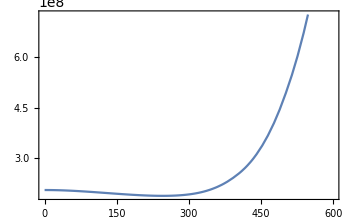

-Graphics-

```mathematica
Plot[Vpath[h],{h,0,600}]
Plot[Vpath[h],{h,0,50000}]
```

```mathematica
minSdata1=Table[{h,S/.Minimize[{V0T[h,S],-5000π<S<5000π},S][[2]]}
,{h,10^-5,300,1}];
minSdata2=Table[{h,S/.Minimize[{V0T[h,S],-5000π<S<5000π},S][[2]]}
,{h,300,10000,100}];
minSdata3=Table[{h,S/.Minimize[{V0T[h,S],-5000π<S<5000π},S][[2]]}
,{h,11000,100000,1000}];
```

```mathematica
minSdata=Join[minSdata1,minSdata2,minSdata3];
Spathnum[h_]=Interpolation[minSdata][h];
```

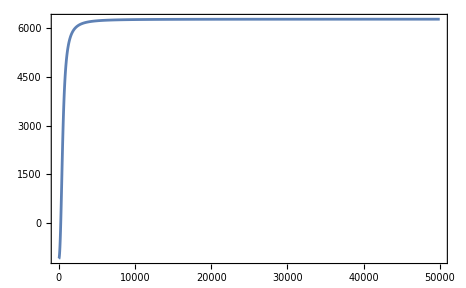

```mathematica
Plot[Spathnum[h],{h,0,50000},PlotRange->Full]
```

#### Simplified model

```mathematica
V‵Sim‵0=-1/2 μHsq h^2+1/4 λ h^4-1/2 A S (h^2-2 v^2)+1/2 μSsq S^2;
sol‵tree‵sim={A->(Sin[θ]Cos[θ](mh^2-mS^2))/(√2 v),μSsq->1/2(Cos[2θ](mS^2-mh^2)+mh^2+mS^2),λ->(Cos[2θ](mh^2-mS^2)+mh^2+mS^2)/(8 v^2),μHsq->1/4(Cos[2θ](mh^2-mS^2)+mh^2+mS^2)};
```

```mathematica
massmatrix‵sim=D[V‵Sim‵0,{{h,S},2}]//Simplify;
mgs‵sim=λ h^2-μHsq-A S;
```

```mathematica
{mSsq,mhsq}=Eigenvalues[massmatrix‵sim]//Simplify;
```

```mathematica
VCW‵Sim[h_,S_]:=1/(64 π^2)(6 mWsq[h]^2(Log[mWsq[h]/mZ^2]-5/6)+3 mZsq[h]^2(Log[mZsq[h]/mZ^2]-5/6)-12 mtsq[h]^2(Log[mtsq[h]/mZ^2]-3/2)+3(mgs‵sim)^2(Log[(mgs‵sim)/mZ^2]-3/2)+mhsq^2(Log[mhsq/mZ^2]-3/2)+mSsq^2(Log[mSsq/mZ^2]-3/2));
```

```mathematica
V0Tpre‵sim[h_,S_]=V‵Sim‵0+VCW‵Sim[h,S]/.{v->v/(√2)}/.{v->vnum}//Simplify
```

1/64 (1/(8 π^2)((√(A^2 (4 h^2+S^2)+2 A S (-3 h^2 λ+μ_H^2+μ_S^2)+(-3 h^2 λ+μ_H^2+μ_S^2)^2)+A S-3 h^2 λ+μ_H^2-μ_S^2)^2 (2 log(0.000060131 (-√(A^2 (4 h^2+S^2)+2 A S (-3 h^2 λ+μ_H^2+μ_S^2)+(-3 h^2 λ+μ_H^2+μ_S^2)^2)-A S+3 h^2 λ-μ_H^2+μ_S^2))-3)+(√(A^2 (4 h^2+S^2)+2 A S (-3 h^2 λ+μ_H^2+μ_S^2)+(-3 h^2 λ+μ_H^2+μ_S^2)^2)-A S+3 h^2 λ-μ_H^2+μ_S^2)^2 (2 log(0.000060131 (√(A^2 (4 h^2+S^2)+2 A S (-3 h^2 λ+μ_H^2+μ_S^2)+(-3 h^2 λ+μ_H^2+μ_S^2)^2)-A S+3 h^2 λ-μ_H^2+μ_S^2))-3)+24. (A S-1. h^2 λ+μ_H^2)^2 (1. log(-0.000120262 A S+0.000120262 h^2 λ-0.000120262 μ_H^2)-1.5)+1.07775 h^4 (log(h)-6.05195)+0.912631 h^4 (log(h)-5.92024)-43.8725 h^4 (log(h)-5.63197))-32. A (h^2-60624.1) S+16 h^4 λ-32 h^2 μ_H^2+32 S^2 μ_S^2)

```mathematica
mass‵matrix‵sim=D[V0Tpre‵sim[h,S]//Simplify,{{h,S},2}]/.{h->vnum,S->0};
der‵1loop‵sim=D[V0Tpre‵sim[h,S],{{h,S}}]/.{h->vnum,S->0};
P={{Cos[θ],Sin[θ]},{-Sin[θ],Cos[θ]}};
Diag‵mass={{mhpole^2,0},{0,mS^2}};
rotated=P.Diag‵mass.Inverse[P]//Simplify;
```

```mathematica
benchmark={θ->ArcSin[0.1],mS->5};
mass‵matrix‵sim‵num=mass‵matrix‵sim/.benchmark//N//Simplify;
rotated‵num=rotated/.benchmark//N//Simplify;
der‵1loop‵sim‵num=der‵1loop‵sim/.benchmark//N//Simplify;
```

```mathematica
eqns={rotated‵num[[1,1]]==mass‵matrix‵sim‵num[[1,1]],rotated‵num[[1,2]]==mass‵matrix‵sim‵num[[1,2]],rotated‵num[[2,2]]==mass‵matrix‵sim‵num[[2,2]],der‵1loop‵sim‵num[[1]]==0};
```

```mathematica
{λ1,A1,μH1,μS1}={λ,A,μHsq,μSsq}/.FindRoot[eqns,{{λ,0.14},{A,11.},{μHsq,8800},{μSsq,200}}]//Re;
sol‵1loop={λ->λ1,A->A1,μHsq->μH1,μSsq->μS1}
```

{λ→0.149505,A→6.363,μ_H^2→8765.52,μ_S^2→182.504}

```mathematica
V0T‵Sim[h_,S_]=V0Tpre‵sim[h,S]/.sol‵1loop//Re//Simplify
```

0.0373764 h^4+h^2 (-3.1815 S-4382.76)+0.000197893 Re(1.07775 h^4 (log(h)-6.05195)+0.912631 h^4 (log(h)-5.92024)-43.8725 h^4 (log(h)-5.63197)+0.536445 (-1. h^2+42.5603 S+58630.1)^2 (1. log(0.0000179798 h^2-0.000765227 S-1.05416)-1.5)+(-0.448516 h^2+√(0.201167 h^4+h^2 (-5.70782 S-7864.72)+40.4878 S^2+113873. S+8.00672×10^7)+6.363 S+8583.02)^2 (2 log(0.0000269697 h^2-0.000060131 √(0.201167 h^4+h^2 (-5.70782 S-7864.72)+40.4878 S^2+113873. S+8.00672×10^7)-0.000382614 S-0.516106)-3)+(0.448516 h^2+√(0.201167 h^4+h^2 (-5.70782 S-7864.72)+40.4878 S^2+113873. S+8.00672×10^7)-6.363 S-8583.02)^2 (2 log(0.0000269697 h^2+0.000060131 √(0.201167 h^4+h^2 (-5.70782 S-7864.72)+40.4878 S^2+113873. S+8.00672×10^7)-0.000382614 S-0.516106)-3))+S (91.2521 S+192876.)

```mathematica
mindata1sim=Table[{h,Minimize[{V0T‵Sim[h,S]},S][[1]]}
,{h,10^-5,300,1}];
mindata2sim=Table[{h,Minimize[{V0T‵Sim[h,S]},S][[1]]}
,{h,300,10000,100}];
mindata3sim=Table[{h,Minimize[{V0T‵Sim[h,S]},S][[1]]}
,{h,11000,100000,1000}];
```

```mathematica
mindatasim=Join[mindata1sim,mindata2sim,mindata3sim];
Vpathsim[h_]=Interpolation[mindatasim][h];
```

```mathematica
Vpathsim0[h_]=Vpathsim[h]-Vpathsim[0];
Vpath0[h_]=Vpath[h]-Vpath[0];
```

```mathematica
mindataS1sim=Table[{h,S/.Minimize[{V0T‵Sim[h,S]},S][[2]]}
,{h,10^-5,300,1}];
mindataS2sim=Table[{h,S/.Minimize[{V0T‵Sim[h,S]},S][[2]]}
,{h,300,10000,100}];
mindataS3sim=Table[{h,S/.Minimize[{V0T‵Sim[h,S]},S][[2]]}
,{h,11000,100000,1000}];
```

```mathematica
mindataSsim=Join[mindataS1sim,mindataS2sim,mindataS3sim];
Spathnumsim[h_]=Interpolation[mindataSsim][h];
```

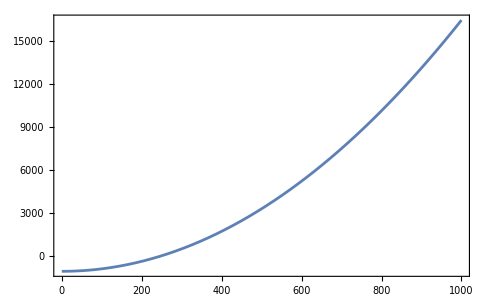

```mathematica
Plot[Spathnumsim[h],{h,0,1000},PlotRange->Full]
```

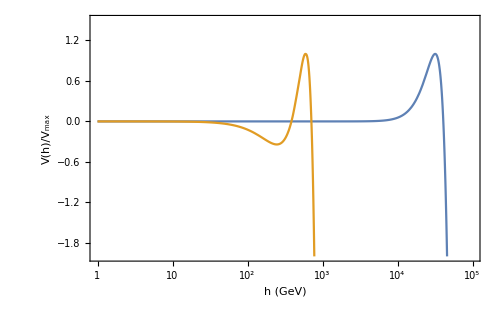

```mathematica
Plot[{Vpath0[10^logh]/maxalp,Vpathsim0[10^logh]/maxsim},{logh,0,5},PlotRange->{Full,{-2,1.5}},BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,FrameLabel->{Style["h (GeV)",FontFamily->"Times",FontSize->22],Style["V(h)/V_max",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],ImageSize->500,FrameTicks->{{None,None},{LogTicks[0,6,1],True}},Epilog->{Inset[Framed[Column[{LineLegend[{ColorData[97,1],ColorData[97,2]},{Style["ALP",FontSize->18,FontFamily->"Times"],Style["Simplified",FontSize->18,FontFamily->"Times"]}]}],RoundingRadius->5],Scaled[{0.2,0.8}]]}]
```

-Graphics-

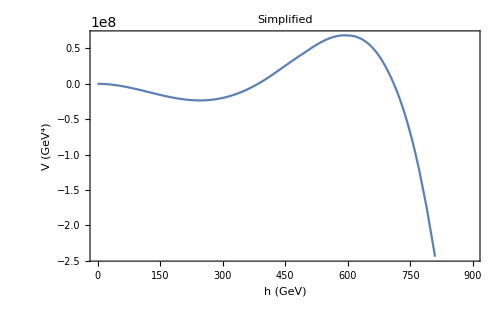

```mathematica
Plot[Vpath0[h],{h,0,40000},BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,FrameLabel->{Style["h (GeV)",FontFamily->"Times",FontSize->22],Style["V (GeV^4)",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],ImageSize->500,PlotLabel->Style["ALP",FontSize->24,FontFamily->"Times"]]
Plot[Vpathsim0[h],{h,0,900},BaseStyle->{FontSize->22,FontFamily->"Times"},Frame->True,FrameLabel->{Style["h (GeV)",FontFamily->"Times",FontSize->22],Style["V (GeV^4)",FontFamily->"Times",FontSize->24]},LabelStyle->{Black},FrameTicksStyle->Directive[FontFamily->"Times",FontSize->24],ImageSize->500,PlotLabel->Style["Simplified",FontSize->24,FontFamily->"Times"]]
```